```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Temp\VM2D-ICVFM-2026-01-10\settings\airfoils

```mathematica
SplitLine[a_List,b_List,h_,OptionsPattern[{FirstPoint->True,LastPoint->True}]]:=Module[{dr,np,i,j},np=Ceiling[Norm[b-a]/h];dr=(b-a)/np;(*Print[np];Print[dr];*)
i=If[OptionValue[FirstPoint],0,1];
j=If[OptionValue[LastPoint],np,np-1];
Table[a+q dr,{q,i,j}]]
```

```mathematica
(*Расширяющаяся труба - задача для внутреннего течения*)
(*pts={{6.3,0},{6.3,0.6},{-0.2,0.6},{-0.5,0.3},{-3.5,0.3},{-3.5,0},{-3.5,-0.3},{-0.5,-0.3},{-0.2,-0.6},{6.3,-0.6},{6.3,0}};
h=π/400.;*)
```

```mathematica
(*Прямоугольный профиль - из эксперимента А.Н.Нуриева*)
(*pts={{0.05,0.0},{0.05,0.5},{-0.05,0.5},{-0.05,0.0},{-0.05,-0.5},{0.05,-0.5},{0.05,0.0}};
h=0.1/20.;*)
```

```mathematica
(*Профиль с заостренными концами - из эксперимента А.Н.Нуриева*)
(*H=√(0.1^2-0.05^2)
pts={{0.05,0.0},{0.05,0.5-H},{0.0,0.5},{-0.05,0.5-H},{-0.05,0.0},{-0.05,-0.5+H},{0.0,-0.5},{0.05,-0.5+H},{0.05,0.0}};
h=0.1/20.;*)
```

```mathematica
(*Прямоугольный профиль - из эксперимента В.А.Фролова*)
(*pts={{0.25,0.0},{0.25,0.025},{-0.25,0.025},{-0.25,0.0},{-0.25,-0.025},{0.25,-0.025},{0.25,0.0}};
h=π/100.;*)
```

```mathematica
(*Тонкая пластинка - для Моргенталя*)
(*pts={{16.5,0.0},{16.5,0.165},{-16.5,0.165},{-16.5,0.0},{-16.5,-0.165},{16.5,-0.165},{16.5,0.0}};
h=0.16/8.;*)
```

```mathematica
(*Профиль моста StructureA - для Моргенталя*)
(*pts={{16.5,0.0},{13.3,1.425},{-13.3,1.425},{-16.5,0.0},{-13.3,-1.425},{13.3,-1.425},{16.5,0.0}};
h=0.16/(2 8.);*)
```

```mathematica
(*Профиль моста StructureH - для Моргенталя*)
(*pts={{6.0,0.0},{6.0,1.2},{5.6,1.2},{5.6,0.2},{-5.6,0.2},{-5.6,1.2},{-6.0,1.2},{-6.0,0.0},{-6.0,-1.2},{-5.6,-1.2},{-5.6,-0.2},{5.6,-0.2},{5.6,-1.2},{6.0,-1.2},{6.0,0.0}};
h=0.06/8.;*)
```

```mathematica
(*Сапсан*)
```

```mathematica
(*pts={{127.36293,0.00000},{127.36384,0.14918},{127.35683,0.29820},{127.34849,0.37709},{127.33546,0.45535},{127.00295,0.99251},{126.40812,1.24854},{124.85860,1.46366},{123.29882,1.59231},{113.13441,1.59231},{102.97000,1.59231},{102.97000,1.16241},{102.97000,0.73250},{102.64000,0.73250},{102.31000,0.73250},{102.31000,1.16241},{102.31000,1.59231},{89.81000,1.59231},{77.31000,1.59231},{77.31000,1.16241},{77.31000,0.73250},{76.98000,0.73250},{76.65000,0.73250},{76.65000,1.16241},{76.65000,1.59231},{64.15000,1.59231},{51.65000,1.59231},{51.65000,1.16241},{51.65000,0.73250},{51.32000,0.73250},{50.99000,0.73250},{50.99000,1.16241},{50.99000,1.59231},{38.49000,1.59231},{25.99000,1.59231},{25.99000,1.16241},{25.99000,0.73250},{25.66000,0.73250},{25.33000,0.73250},{25.33000,1.16241},{25.33000,1.59231},{12.83000,1.59231},{0.33000,1.59231},{0.33000,1.16241},{0.33000,0.73250},{0.16500,0.73250},{0.00000,0.73250},{-0.16500,0.73250},{-0.33000,0.73250},{-0.33000,1.16241},{-0.33000,1.59231},{-12.83000,1.59231},{-25.33000,1.59231},{-25.33000,1.16241},{-25.33000,0.73250},{-25.66000,0.73250},{-25.99000,0.73250},{-25.99000,1.16241},{-25.99000,1.59231},{-38.49000,1.59231},{-50.99000,1.59231},{-50.99000,1.16241},{-50.99000,0.73250},{-51.32000,0.73250},{-51.65000,0.73250},{-51.65000,1.16241},{-51.65000,1.59231},{-64.15000,1.59231},{-76.65000,1.59231},{-76.65000,1.16241},{-76.65000,0.73250},{-76.98000,0.73250},{-77.31000,0.73250},{-77.31000,1.16241},{-77.31000,1.59231},{-89.81000,1.59231},{-102.31000,1.59231},{-102.31000,1.16241},{-102.31000,0.73250},{-102.64000,0.73250},{-102.97000,0.73250},{-102.97000,1.16241},{-102.97000,1.59231},{-113.13441,1.59231},{-123.29882,1.59231},{-124.85860,1.46366},{-126.40812,1.24854},{-127.00295,0.99251},{-127.33546,0.45535},{-127.34849,0.37709},{-127.35683,0.29820},{-127.36384,0.14918},{-127.36293,0.00000},{-127.36384,-0.14918},{-127.35683,-0.29820},{-127.34849,-0.37709},{-127.33546,-0.45535},{-127.00295,-0.99251},{-126.40812,-1.24854},{-124.85860,-1.46366},{-123.29882,-1.59231},{-113.13441,-1.59231},{-102.97000,-1.59231},{-102.97000,-1.16241},{-102.97000,-0.73250},{-102.64000,-0.73250},{-102.31000,-0.73250},{-102.31000,-1.16241},{-102.31000,-1.59231},{-89.81000,-1.59231},{-77.31000,-1.59231},{-77.31000,-1.16241},{-77.31000,-0.73250},{-76.98000,-0.73250},{-76.65000,-0.73250},{-76.65000,-1.16241},{-76.65000,-1.59231},{-64.15000,-1.59231},{-51.65000,-1.59231},{-51.65000,-1.16241},{-51.65000,-0.73250},{-51.32000,-0.73250},{-50.99000,-0.73250},{-50.99000,-1.16241},{-50.99000,-1.59231},{-38.49000,-1.59231},{-25.99000,-1.59231},{-25.99000,-1.16241},{-25.99000,-0.73250},{-25.66000,-0.73250},{-25.33000,-0.73250},{-25.33000,-1.16241},{-25.33000,-1.59231},{-12.83000,-1.59231},{-0.33000,-1.59231},{-0.33000,-1.16241},{-0.33000,-0.73250},{-0.16500,-0.73250},{0.00000,-0.73250},{0.16500,-0.73250},{0.33000,-0.73250},{0.33000,-1.16241},{0.33000,-1.59231},{12.83000,-1.59231},{25.33000,-1.59231},{25.33000,-1.16241},{25.33000,-0.73250},{25.66000,-0.73250},{25.99000,-0.73250},{25.99000,-1.16241},{25.99000,-1.59231},{38.49000,-1.59231},{50.99000,-1.59231},{50.99000,-1.16241},{50.99000,-0.73250},{51.32000,-0.73250},{51.65000,-0.73250},{51.65000,-1.16241},{51.65000,-1.59231},{64.15000,-1.59231},{76.65000,-1.59231},{76.65000,-1.16241},{76.65000,-0.73250},{76.98000,-0.73250},{77.31000,-0.73250},{77.31000,-1.16241},{77.31000,-1.59231},{89.81000,-1.59231},{102.31000,-1.59231},{102.31000,-1.16241},{102.31000,-0.73250},{102.64000,-0.73250},{102.97000,-0.73250},{102.97000,-1.16241},{102.97000,-1.59231},{113.13441,-1.59231},{123.29882,-1.59231},{124.85860,-1.46366},{126.40812,-1.24854},{127.00295,-0.99251},{127.33546,-0.45535},{127.34849,-0.37709},{127.35683,-0.29820},{127.36384,-0.14918},{127.36293,0.00000}};
h=0.20;*)
```

```mathematica
pt1=Cases[0.5{Cos@#,Sin@#}&/@Range[0,2π-π/200,π/200],{x_,y_}/;(x>1/4 (-3+√5)&&y>=0)]
```

{{0.5,0.},{0.499938,0.00785366},{0.499753,0.0157054},{0.499445,0.0235532},{0.499013,0.0313953},{0.498459,0.0392295},{0.497781,0.0470542},{0.49698,0.0548672},{0.496057,0.0626666},{0.495012,0.0704506},{0.493844,0.0782172},{0.492555,0.0859646},{0.491144,0.0936907},{0.489611,0.101394},{0.487958,0.109072},{0.486185,0.116723},{0.484292,0.124345},{0.482279,0.131937},{0.480147,0.139496},{0.477897,0.14702},{0.475528,0.154508},{0.473043,0.161959},{0.47044,0.169369},{0.467722,0.176737},{0.464888,0.184062},{0.46194,0.191342},{0.458877,0.198574},{0.455702,0.205757},{0.452414,0.21289},{0.449014,0.21997},{0.445503,0.226995},{0.441883,0.233965},{0.438153,0.240877},{0.434316,0.247729},{0.430371,0.254521},{0.42632,0.261249},{0.422164,0.267913},{0.417904,0.274511},{0.41354,0.281042},{0.409075,0.287503},{0.404508,0.293893},{0.399842,0.30021},{0.395078,0.306454},{0.390215,0.312621},{0.385257,0.318712},{0.380203,0.324724},{0.375056,0.330656},{0.369816,0.336506},{0.364484,0.342274},{0.359063,0.347956},{0.353553,0.353553},{0.347956,0.359063},{0.342274,0.364484},{0.336506,0.369816},{0.330656,0.375056},{0.324724,0.380203},{0.318712,0.385257},{0.312621,0.390215},{0.306454,0.395078},{0.30021,0.399842},{0.293893,0.404508},{0.287503,0.409075},{0.281042,0.41354},{0.274511,0.417904},{0.267913,0.422164},{0.261249,0.42632},{0.254521,0.430371},{0.247729,0.434316},{0.240877,0.438153},{0.233965,0.441883},{0.226995,0.445503},{0.21997,0.449014},{0.21289,0.452414},{0.205757,0.455702},{0.198574,0.458877},{0.191342,0.46194},{0.184062,0.464888},{0.176737,0.467722},{0.169369,0.47044},{0.161959,0.473043},{0.154508,0.475528},{0.14702,0.477897},{0.139496,0.480147},{0.131937,0.482279},{0.124345,0.484292},{0.116723,0.486185},{0.109072,0.487958},{0.101394,0.489611},{0.0936907,0.491144},{0.0859646,0.492555},{0.0782172,0.493844},{0.0704506,0.495012},{0.0626666,0.496057},{0.0548672,0.49698},{0.0470542,0.497781},{0.0392295,0.498459},{0.0313953,0.499013},{0.0235532,0.499445},{0.0157054,0.499753},{0.00785366,0.499938},{0.,0.5},{-0.00785366,0.499938},{-0.0157054,0.499753},{-0.0235532,0.499445},{-0.0313953,0.499013},{-0.0392295,0.498459},{-0.0470542,0.497781},{-0.0548672,0.49698},{-0.0626666,0.496057},{-0.0704506,0.495012},{-0.0782172,0.493844},{-0.0859646,0.492555},{-0.0936907,0.491144},{-0.101394,0.489611},{-0.109072,0.487958},{-0.116723,0.486185},{-0.124345,0.484292},{-0.131937,0.482279},{-0.139496,0.480147},{-0.14702,0.477897},{-0.154508,0.475528},{-0.161959,0.473043},{-0.169369,0.47044},{-0.176737,0.467722},{-0.184062,0.464888}}

```mathematica
pt2=Reverse@Table[{x,1/2 (-1+√5)√(x+0.75)},{x,-0.75,1/4 (-3+√5),π/300}]
```

{{-0.194985,0.460431},{-0.205457,0.456067},{-0.215929,0.45166},{-0.226401,0.44721},{-0.236873,0.442715},{-0.247345,0.438175},{-0.257817,0.433586},{-0.268289,0.428949},{-0.278761,0.424261},{-0.289233,0.41952},{-0.299705,0.414726},{-0.310177,0.409875},{-0.320649,0.404966},{-0.331121,0.399997},{-0.341593,0.394965},{-0.352065,0.389869},{-0.362537,0.384705},{-0.373009,0.37947},{-0.383481,0.374163},{-0.393953,0.368779},{-0.404425,0.363315},{-0.414897,0.357768},{-0.425369,0.352134},{-0.435841,0.346408},{-0.446313,0.340585},{-0.456785,0.334661},{-0.467257,0.328631},{-0.477729,0.322488},{-0.488201,0.316225},{-0.498673,0.309836},{-0.509145,0.303313},{-0.519617,0.296646},{-0.530089,0.289825},{-0.54056,0.282841},{-0.551032,0.275679},{-0.561504,0.268326},{-0.571976,0.260766},{-0.582448,0.25298},{-0.59292,0.244947},{-0.603392,0.236641},{-0.613864,0.228033},{-0.624336,0.219087},{-0.634808,0.20976},{-0.64528,0.199998},{-0.655752,0.189735},{-0.666224,0.178884},{-0.676696,0.167331},{-0.687168,0.154918},{-0.69764,0.14142},{-0.708112,0.12649},{-0.718584,0.109544},{-0.729056,0.089442},{-0.739528,0.0632451},{-0.75,0.}}

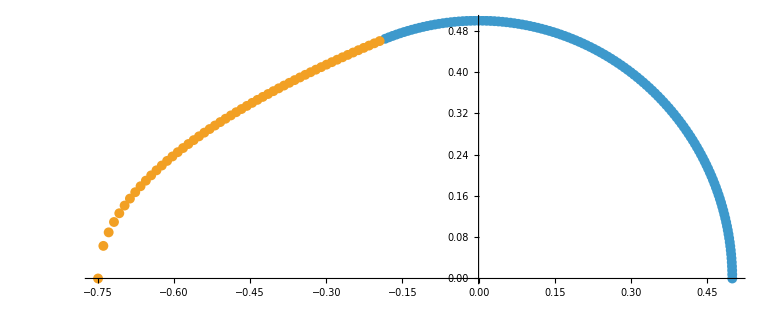

```mathematica
ListPlot[{pt1,pt2},AspectRatio->Automatic]
```

```mathematica
pts=pt1~Join~pt2~Join~(Reverse[pt2/.{x_,y_}:>{x,-y}][[2;;]])~Join~Reverse[pt1/.{x_,y_}:>{x,-y}];
h=1;
```

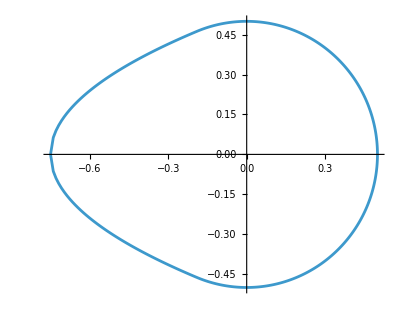

```mathematica
ListLinePlot[pts,AspectRatio->Automatic]
```

```mathematica
vertex=Flatten[Table[SplitLine[pts[[i]],pts[[i+1]],h,LastPoint->False],{i,Length@pts-1}],1];
```

```mathematica
n=Length@vertex
```

356

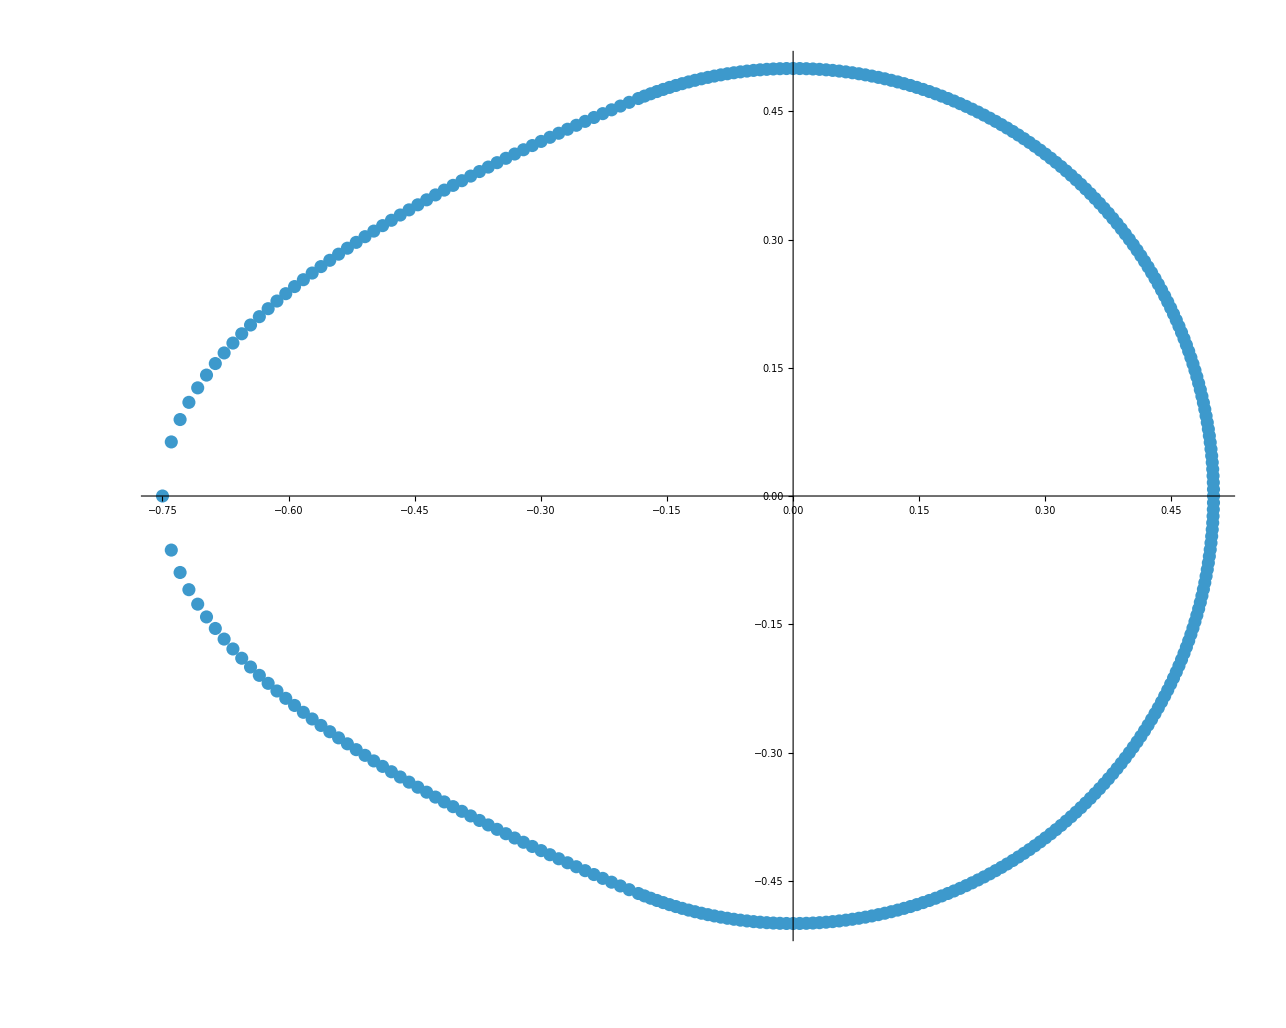

```mathematica
ListPlot[vertex,AspectRatio->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["pear",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.12   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2024/01/14     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2024 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |
*-----------------------------------------------------------------------------*
| File name: pear"<>StringRepeat[" ",49]<>"|
| Info: pear ("<>TextString[n]<>" panels)"<>StringRepeat[" ",34-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/ 
"}~Join~{"geometry = {"}
~Join~
Table[{"{",TextString@vertex[[i,1]],",",TextString@vertex[[i,2]],", i},"},{i,n-1}]
~Join~
{{"{",TextString@vertex[[-1,1]],",",TextString@vertex[[-1,2]],", i}"}}
~Join~
{{"};"}}
,"Table"]
```

pear